```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
(*this is the length of the one-dimensional mesh[1]*)
L1=1.2444414542953002;
r=0.2;
cr={0.45,0.55};
NN=13;
Δθ=2π/NN;
Δl=2 r Sin[Δθ/2];
```

```mathematica
tabr=Table[cr +r{Cos[n Δθ],Sin[n Δθ]},{n,0,NN}];
```

```mathematica
tabr
```

{{0.65,0.55},{0.627091,0.642945},{0.563613,0.714597},{0.474107,0.748542},{0.379079,0.737003},{0.300298,0.682625},{0.255812,0.597863},{0.255812,0.502137},{0.300298,0.417375},{0.379079,0.362997},{0.474107,0.351458},{0.563613,0.385403},{0.627091,0.457055},{0.65,0.55}}

```mathematica
v2d[x_]:={1-x[[1]] + 2 x[[2]]^2,1-4x[[1]]^2 + 2 x[[2]]^2, Cos[2 π x[[1]]]}
vline[x_]:={1-x,1-4x^2 , Sin[2 π x]}
```

```mathematica
component=2;
```

```mathematica
t2d=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/nodal_values/v_2d.csv"][[2;;]];
t2d=Table[{t2d[[i,4]],t2d[[i,5]],t2d[[i,component]]},{i,2,Length[t2d]}]
```

{{0.255812,0.597863,1.45312},{0.353021,0.637298,1.3138},{0.379079,0.737003,1.51154},{0.341587,0.553747,1.14654},{0.255812,0.502137,1.24252},{0.404764,0.592076,1.04577},{0.436586,0.660476,1.11003},{0.474107,0.748542,1.22152},{0.362864,0.462772,0.901635},{0.300298,0.417375,0.987689},{0.415471,0.51941,0.849109},{0.472624,0.567857,0.75143},{0.5333,0.623797,0.640612},{0.563613,0.714597,0.750659},{0.501901,0.686853,0.935913},{0.379079,0.362997,0.68873},{0.43749,0.433413,0.610104},{0.491712,0.486346,0.505943},{0.558053,0.523367,0.302133},{0.592111,0.585027,0.282132},{0.627091,0.642945,0.253782},{0.474107,0.351458,0.347935},{0.50119,0.415023,0.339723},{0.558053,0.454273,0.167035},{0.627091,0.457055,-0.155174},{0.65,0.55,-0.085},{0.563613,0.385403,0.0264331}}

```mathematica
tline=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/three_domains/solution/nodal_values/v_line.csv"][[2;;]];
tline=Table[{tline[[i,4]],tline[[i,component]]},{i,2,Length[tline]}]
```

{{1.14872,-4.27819},{1.05299,-3.43514},{0.957263,-2.66541},{0.861536,-1.96898},{0.76581,-1.34586},{0.670084,-0.79605},{0.574358,-0.319547},{0.478631,0.0836482},{0.382905,0.413535},{0.287179,0.670113},{0.191453,0.853384},{0.0957263,0.963346},{0.,-5.19454}}

```mathematica
plot2d=ListPointPlot3D[t2d,PlotStyle->{Red,PointSize->0.01}]
```

-Graphics3D-

```mathematica
Show[Plot3D[v2d[{x,y}][[component]],{x,0,L},{y,0,h}],plot2d]
```

-Graphics3D-

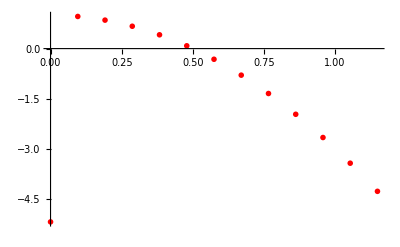

```mathematica
plottline=ListPlot[tline,PlotStyle->{Red,PointSize->0.01}]
```

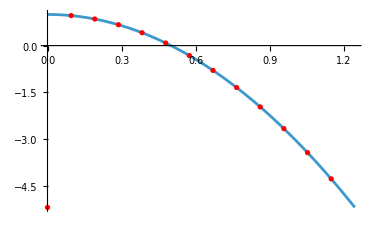

```mathematica
Show[Plot[vline[x][[component]],{x,0,L1}],plottline]
```